```mathematica
ClearAll["Global`*"]
```

# 3DOIT ζ_(4b)

```mathematica
e=1.60 10^-19;
m=6.65 10^-26;
Ω=6 10^9;
r0=3 10^-3;
V0=200;
U0=1 10^-6;

a=A[e,U0,m,r0,Ω];
q=Q[e,V0,m,r0,Ω];
β=5 10^-3;

NoP=6;
time=30000;

Q[e_,V0_,m_,r0_,Ω_]:=(2 e V0)/(m r0^4 Ω^2);
A[e_,U0_,m_,r0_,Ω_]:=(2 e U0)/(m r0^4 Ω^2);


EQS[α_]:=Table[{Subscript[x, i]''[τ]==(α+2 q Cos[2τ])(6 Subscript[x, i][τ]Subscript[y, i][τ]Subscript[z, i][τ])-β Subscript[x, i]'[τ],
Subscript[y, i]''[τ]==(α+2 q Cos[2τ])(3(Subscript[x, i][τ])^2 Subscript[z, i][τ]-(Subscript[z, i][τ])^3)-β Subscript[y, i]'[τ],
Subscript[z, i]''[τ]==(α+2 q Cos[2τ])(3(Subscript[x, i][τ])^2 Subscript[y, i][τ]-3 Subscript[y, i][τ](Subscript[z, i][τ])^2)-β Subscript[z, i]'[τ]},{i,1,NoP}];

INI[α_]:={Subscript[x, 1]'[0]==0,Subscript[y, 1]'[0]==0,Subscript[z, 1]'[0]==0,
Subscript[x, 1][0]==-(√α)/(√2 3^0.25 q),Subscript[y, 1][0]==-(√2 √α)/(3 3^0.25 q),Subscript[z, 1][0]==-(√α)/(√2 3^0.75 q),
Subscript[x, 2]'[0]==0,Subscript[y, 2]'[0]==0,Subscript[z, 2]'[0]==0,
Subscript[x, 2][0]==(√α)/(√2 3^0.25 q),Subscript[y, 2][0]==-(√2 √α)/(3 3^0.25 q),Subscript[z, 2][0]==-(√α)/(√2 3^0.75 q),
Subscript[x, 3]'[0]==0,Subscript[y, 3]'[0]==0,Subscript[z, 3]'[0]==0,
Subscript[x, 3][0]==-(√α)/(√2 3^0.25 q),Subscript[y, 3][0]==(√2 √α)/(3 3^0.25 q),Subscript[z, 3][0]==(√α)/(√2 3^0.75 q),
Subscript[x, 4]'[0]==0,Subscript[y, 4]'[0]==0,Subscript[z, 4]'[0]==0,
Subscript[x, 4][0]==(√α)/(√2 3^0.25 q),Subscript[y, 4][0]==(√2 √α)/(3 3^0.25 q),Subscript[z, 4][0]==(√α)/(√2 3^0.75 q),
Subscript[x, 5]'[0]==0,Subscript[y, 5]'[0]==0,Subscript[z, 5]'[0]==0,
Subscript[x, 5][0]==0,Subscript[y, 5][0]==(√2 √α)/(3 3^0.25 q),Subscript[z, 5][0]==-(2 √α)/(√2 3^0.75 q),
Subscript[x, 6]'[0]==0,Subscript[y, 6]'[0]==0,Subscript[z, 6]'[0]==0,
Subscript[x, 6][0]==0,Subscript[y, 6][0]==-(√2 √α)/(3 3^0.25 q),Subscript[z, 6][0]==(2 √α)/(√2 3^0.75 q)};

VAR=Flatten[Table[{Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,1,NoP}]];

NDS[α_]:=NDSolveValue[{EQS[α],INI[α]},VAR,{τ,0,time}];
solns=NDS[0.1]
```

{InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>],InterpolatingFunction[{{0., 30000.}}, <>]}

```mathematica
ParametricPlot3D[{solns[[1]][t],solns[[2]][t],solns[[3]][t]},{t,0,time}]
```

-Graphics3D-

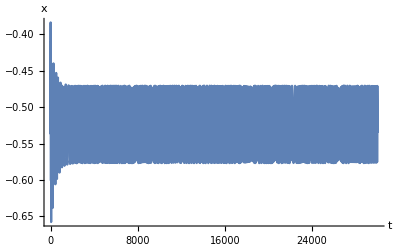

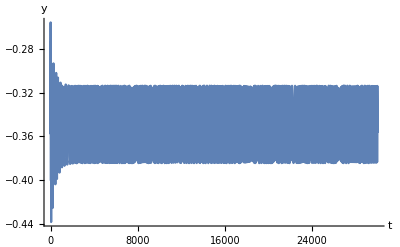

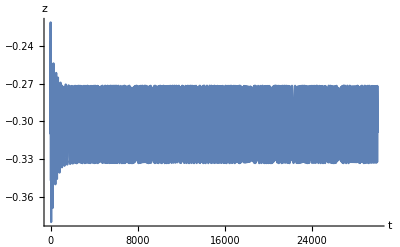

```mathematica
Plot[solns[[1]][t],{t,0,time},AxesLabel->{"t","x"}]
Plot[solns[[2]][t],{t,0,time},AxesLabel->{"t","y"}]
Plot[solns[[3]][t],{t,0,time},AxesLabel->{"t","z"}]
```

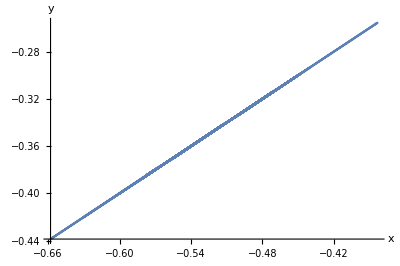

```mathematica
ParametricPlot[{solns[[1]][t],solns[[2]][t]},{t,0,time},AxesLabel->{"x","y"},PlotRangeClipping->False]
```

```mathematica
Options[ParametricPlot]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→Automatic,MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}